```mathematica
list1=Mean/@{{0.111585,0.111585,0.111687},{0.083171,0.083173,0.083400},{0.069200,0.069290,0.069370},{0.060380,0.060360,0.060500},{0.054540,0.054540,0.054530}};
list2=Mean/@{{0.436378,0.437577,0.437890},{0.461957,0.462867,0.463288},{0.471588,0.471968,0.473066},{0.482099,0.483603,0.484213},{0.491393,0.491793,0.491950}};
list3=Mean/@{{0.209550,0.207050,0.209300},{0.379520,0.385210,0.385770},{0.409070,0.407070,0.408010},{0.428220,0.429020,0.429020},{0.432820,0.433820,0.435020}};
list4=Mean/@{{0.056380,0.056580,0.056780},{0.032580,0.031700,0.031470},{0.019250,0.019250,0.019020},{0.011503,0.011210,0.011290},{0.005690,0.005610,0.005400}};
listtemp=Mean/@{{0.054540,0.054540,0.054530},{0.055490,0.055440,0.055440},{0.055850,0.055890,0.055730},{0.056010,0.055930,0.055900},{0.056230,0.056050,0.056000}};
metalist={0.01,0.03,0.05,0.07,0.09};
```

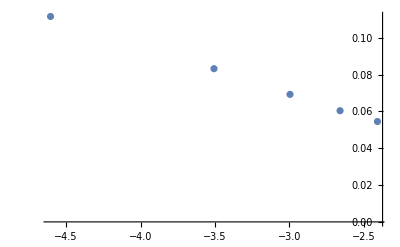
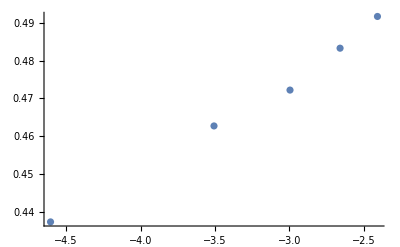
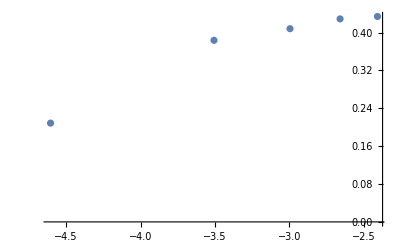
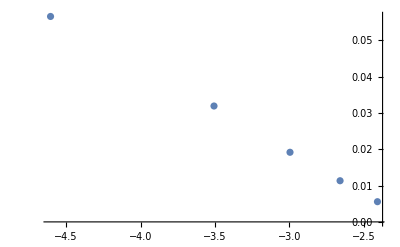

```mathematica
ListPlot[Transpose[{Log@metalist,#}]]&/@{list1,list2,list3,list4}
```

```mathematica
line1=LinearModelFit[Transpose[{Log@metalist,list1}],{1,x},x]
```

FittedModel[-0.00880485-0.0261599 x]

```mathematica
line2=LinearModelFit[Transpose[{Log@metalist,list2}],{1,x},x]
```

FittedModel[0.547491+0.024127 x]

```mathematica
line4=LinearModelFit[Transpose[{Log@metalist,list4}],{1,x},x]
```

FittedModel[-0.0504885-0.0233089 x]

```mathematica
line3=LinearModelFit[Drop[Transpose[{Log@metalist,list3}],1],{1,x},x]
```

FittedModel[0.552076+0.0478942 x]